# JasonB/RectanglePacking

Pack smaller rectangles into a larger rectangle

## Paclet Manifest

"Documentation"

"English"

"Guides"

"RectanglePacking.nb"DocumentationEnglishGuidesRectanglePacking.nb

"ReferencePages"

"Symbols"

"PackRectangles.nb"DocumentationEnglishReferencePagesSymbolsPackRectangles.nb

"RectanglePacker.nb"DocumentationEnglishReferencePagesSymbolsRectanglePacker.nb

"Tutorials"

"Kernel"

"RectanglePackingLibrary.wl"KernelRectanglePackingLibrary.wl

"RectanglePacking.wl"KernelRectanglePacking.wl

"LibraryResources"

"Linux-x86-64"

"RectanglePackingLibrary.so"LibraryResourcesLinux-x86-64RectanglePackingLibrary.so

"MacOSX-x86-64"

"RectanglePackingLibrary.dylib"LibraryResourcesMacOSX-x86-64RectanglePackingLibrary.dylib

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

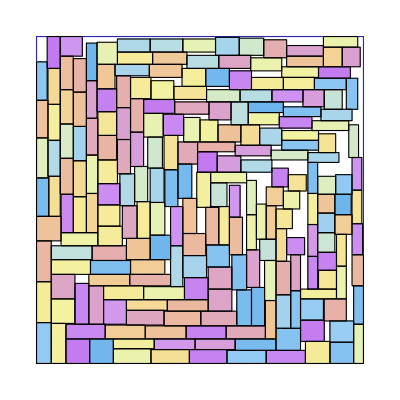

### Basic Description

This paclet contains functions for packing rectangles into a rectangular area, the two-dimensional bin packing problem. No circles, no ovals, hexagons are right out as well. Squares, being a type of rectangle, are also processed, but other quadrilaterals are not.

### Details

Based on the paper "A Thousand Ways to Pack the Bin - A Practical Approach to Two-Dimensional Rectangle Bin Packing." by Jukka Jylänki, which details a number of bin-packing algorithms.

Packing methods include "MaxRects", "Guillotine", "Shelf", and "Skyline", each with variations indicating the heuristics used.

Packing code is implemented in C++ using a modified version of the RectangleBinPack library, and called from the Wolfram Language via LibraryLink.

This paclet is currently in beta until the paclet author can figure out how to build the library on Windows reliably.

### Primary Context

JasonB`RectanglePacking`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad["/Users/jasonb/WolframWorkspaces/LibraryLink_Paclets/RectanglePacking/RectanglePacking"];
```

```mathematica
Needs["JasonB`RectanglePacking`"];
```

### Basic Examples

Pack eight smaller rectangular areas, given as a list of {width, height} pairs, into a 20 by 30 rectangular space:

```mathematica
PackRectangles[{20,30},{{6,9},{5,12},{5,5},{13,11},{5,9},{6,13},{10,6},{6,6}}]
```

{{{0,23},{9,29}},{{0,11},{12,16}},{{6,16},{11,21}},{{0,0},{13,11}},{{9,23},{18,28}},{{13,0},{19,13}},{{12,13},{18,23}},{{0,16},{6,22}}}

Visualize the results:

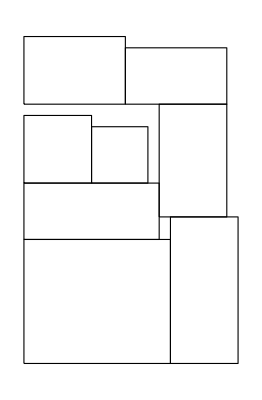

```mathematica
Graphics[{EdgeForm[Black],FaceForm[None],Rectangle@@@%}]
```

### Scope

Create a mutable rectangle packing data structure:

```mathematica
rectp=RectanglePacker[{200,100}]
```

RectanglePacker[12e39eab-5711-4ae2-9d1b-25be6085793e]

Insert some rectangles:

```mathematica
rectp["Insert",RandomInteger[{4,18},{60,2}]]//Short
```

{{{16,18},{33,29}},{{45,80},{54,96}},«56»,{{38,47},{56,51}},{{17,85},{34,99}}}

Visualize the state of the packing object:

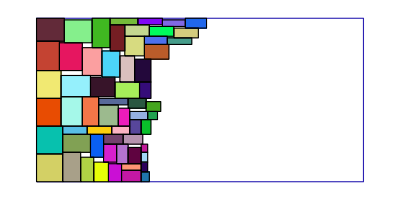

```mathematica
rectp["Graphics"]
```

Add a fixed rectangle:

```mathematica
rectp["PlaceRectangle",Rectangle[{120,20},{150,90}]]
rectp
```

RectanglePacker[12e39eab-5711-4ae2-9d1b-25be6085793e]

Add more rectangles:

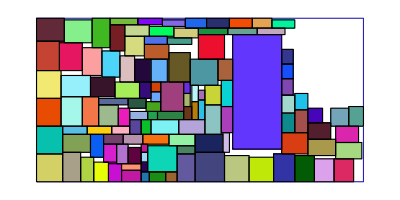

```mathematica
rectp["Insert",RandomInteger[{4,18},{60,2}]];
rectp["Graphics"]
```

Try to insert a rectangle that is too large to fit in the remaining space:

```mathematica
rectp["Insert",{50,50}]
```

PackRectangles::nopac: Failed to pack 1 rectangles.

Failure[…]

```mathematica
rectp=RectanglePacker[{200,100},"Guillotine"];
frames=CreateDataStructure["DynamicArray"];
Until[FailureQ[Quiet[rectp["Insert",RandomInteger[{4,18},2]],PackRectangles::nopac]],frames["Append",rectp["Graphics"]]];
FrameListVideo[Normal[frames],RasterSize->400]
```

## Source & Additional Information

### Creator

Jason Biggs, Wolfram Research

### Source Control Repository

https://github.com/jasondbiggs/RectanglePacking

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

rectangle bin packing

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

A thousand ways to pack the bin-a practical approach to two-dimensional rectangle bin packing. Jukka Jylänki. 2010.  [more info]

RectangleBinPack library, https://github.com/juj/RectangleBinPack

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.